```mathematica
γ=10;
d=40;
αp=2/3;
```

```mathematica
ρp[γ_]:=Log[γ/(γ-1)];
ρπ[λ_,d_,γ_,αp_]:=-Log[(Log[γ/(γ-1)]*(αp*d+1)-λ)/(Log[γ/(γ-1)]*αp*d)];
ρr[λ_,γ_]:=λ*γ;
λc[γ_,αp_,d_]:=Log[γ/(γ-1)]*(αp*d+1);
```

Valori per γ=10, d=20

```mathematica
numπ20:={{1,0.260948},{1.5,0.43413827160493795},{2,0.6066304526749016},{2.5,0.774391358024689},{3,0.93672839506173},{3.5,1.0890958847736527},{4,1.2319843621399207},{4.5,1.3638905349794095},{5,1.4841563786008316},{5.5,1.593271604938268},{6,1.6942201646090442},{6.5,1.7858345679012324},{7,1.8684654320987593},{7.5,1.936673251028804}}
```

```mathematica
nump20:={{1,0.2637934156378596},{1.5,0.2687139917695478},{2,0.2735654320987649},{2.5,0.27856913580246856},{3,0.28389506172839424},{3.5,0.2866037037037035},{4,0.28996296296296337},{4.5,0.29161275720164553},{5,0.2953205761316869},{5.5,0.29717325102880604},{6,0.30034156378600824},{6.5,0.3029094650205759},{7,0.30542757201646087},{7.5,0.30796172839506103}}
```

Valori per γ=2, d=4

```mathematica
numpN:={{1,0.7435818930041169},{2,0.7337333333333359},{3,0.7496596707818934},{4,0.768364609053496},{5,0.8301921810699592},{6,0.788255555555555},{7,0.7995415637860§
76},{8,0.8084761316872427},{9,0.8136526748971191},{10,0.817502880658436}}
numπN:={{1,0.19297777777777775},{2,0.905496296296299},{3,1.5977341563786083},{4,2.2865851851851926},{5,2.953351028806652},{6,3.6856427983539666},{7,4.391172016460882},{8,5.057743621399026},{9,5.736611522633588},{10,6.4043613168724285}}
```

Valori per γ=10, d=40

```mathematica
nump:={{0.2,0.1523800000000002},{0.4,0.14035888888888876},{0.6,0.1431988888888889},{0.8,0.14420777777777774},{1,0.14311222222222209},{1.5,0.1550899999999999},{2,0.16375222222222252}};
numpUnstable:={{3,0.5925555555555563},{4,0.82145777777778},{5,1.0722911111111124},{6,1.365310000000003},{7,1.6908577777777793},{8,2.075045555555557},{9,2.394334444444448},{10,2.523242222222224}};
numπ:={{0.2, 0.019116666666666695},{0.4, 0.09358888888888879},{0.6, 0.16352222222222218},{0.8, 0.23282666666666663},{1, 0.3033877777777774},{1.5, 0.46376111111111085},{2, 0.6055411111111104}};
numπUnstable:={{3, 0.8381499999999995},{4,1.1253444444444458},{5,1.3617900000000012},{6, 1.6159533333333314},{7, 1.9113488888888888},{8, 2.1575455555555574},{9, 2.4765233333333336},{10, 2.681083333333332}};
numr:={{0.2,1.7830655713255688},{0.4,3.947361676511606},{0.6,6.133101460932428},{0.8,7.983506173200949},{1,10.176515166794973},{1.5,15.65399947256519},{2,21.780434169443676}};
```

Valori per γ=10, d=40 version Mod (pseudocode come Mohammad)

```mathematica
numpMod:={{0.2,0.14853555555555537 },{0.4,0.1435555555555557},{0.6,0.14613111111111113},{0.8,0.14859777777777775},{1,0.15512777777777753}};
numpModUnstable:={{1.5,0.2663277777777779},{2,0.48148},{3,0.8053833333333332},{4,1.0323044444444467},{5,1.5287588888888894},{6,1.5370522222222227},{7,2.241785555555559},{8,2.4564700000000017},{9,3.2499644444444526},{10,3.7134722222222285}};
numπMod:={{0.2,0.020073333333333245},{0.4,0.08669222222222239},{0.6,0.14647555555555566},{0.8,0.200472222222222},{1, 0.268176666666666}};
numπModUnstable:={{1.5,  0.36232555555555546},{2, 0.5024355555555556},{3, 0.7624977777777777},{4, 0.9899933333333337},{5, 1.2409633333333334},{6, 1.486952222222223},{7, 1.7756055555555557},{8, 2.0440999999999985},{9, 2.290018888888885},{10, 2.478844444444445}};
```

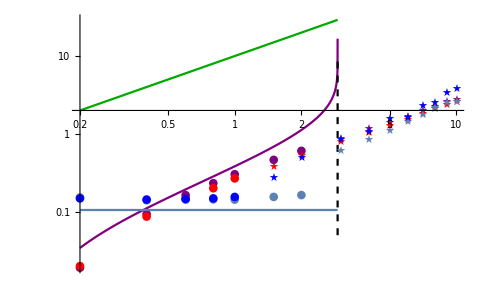

```mathematica
Show[LogLogPlot[ρr[λ,γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Darker[Green]],LogLogPlot[ρπ[λ,d,γ,αp],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Purple],ListLogLogPlot[numπ,PlotStyle->Purple],ListLogLogPlot[numπMod,PlotStyle->Red],ListLogLogPlot[numπUnstable,PlotStyle->Purple,PlotMarkers->"★"],ListLogLogPlot[numπModUnstable,PlotStyle->Red,PlotMarkers->"★"],LogLogPlot[ρp[γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All],ListLogLogPlot[nump],ListLogLogPlot[numpMod,PlotStyle->Blue],ListLogLogPlot[numpUnstable,PlotMarkers->"★"],ListLogLogPlot[numpModUnstable,PlotStyle->Blue,PlotMarkers->"★"],ParametricPlot[{Log[λc[γ,αp,d]],x},{x,Log@0.05,Log@10},PlotStyle->{Black,Dashed}],PlotRange->Full]
```

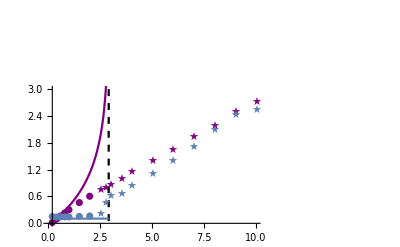

```mathematica
Show[Plot[ρπ[λ,d,γ,αp],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Purple],ListPlot[numπ,PlotStyle->Purple],ListPlot[numπUnstable,PlotStyle->Purple,PlotMarkers->"★"],Plot[ρp[γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All],ListPlot[nump],ListPlot[numpUnstable,PlotMarkers->{"★"}],ParametricPlot[{λc[γ,αp,d],x},{x,0.05,10},PlotStyle->{Black,Dashed}],PlotRange->{{0,10},{0,3}}]
```

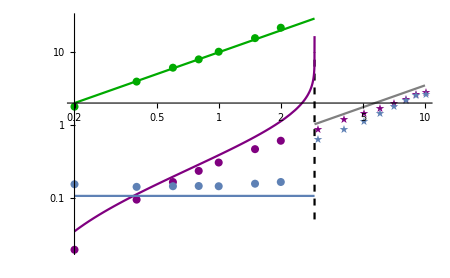

```mathematica
Show[LogLogPlot[ρr[λ,γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Darker[Green]],ListLogLogPlot[numr,PlotStyle->Darker[Green]],LogLogPlot[ρπ[λ,d,γ,αp],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Purple],ListLogLogPlot[numπ,PlotStyle->Purple],ListLogLogPlot[numπUnstable,PlotStyle->Purple,PlotMarkers->"★"],LogLogPlot[ρp[γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All],ListLogLogPlot[nump],ListLogLogPlot[numpUnstable,PlotMarkers->"★"],ParametricPlot[{Log[λc[γ,αp,d]],x},{x,Log@0.05,Log@10},PlotStyle->{Black,Dashed}],LogLogPlot[0.35λ,{λ,λc[γ,αp,d],10},PlotStyle->{Gray}],PlotRange->Full]
```

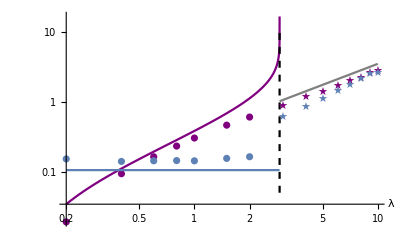

```mathematica
Show[%22,AxesLabel->{HoldForm[λ],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
{3,0.5925555555555563},{4,0.82145777777778},{5,1.0722911111111124},{6,1.365310000000003},{7,1.6908577777777793},{8,2.075045555555557},{9,2.394334444444448},{10,2.523242222222224}
```

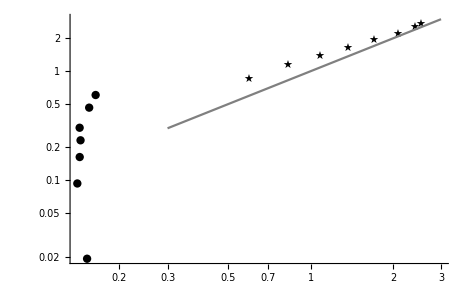

```mathematica
Show[ListLogLogPlot[{{0.1523800000000002, 0.019116666666666695},{0.14035888888888876, 0.09358888888888879},{0.1431988888888889, 0.16352222222222218},{0.14420777777777774, 0.23282666666666663},{0.14311222222222209, 0.3033877777777774},{0.1550899999999999, 0.46376111111111085},{0.16375222222222252, 0.6055411111111104}},PlotStyle->Black],ListLogLogPlot[{{0.5925555555555563, 0.8381499999999995},{0.82145777777778,1.1253444444444458},{1.0722911111111124,1.3617900000000012},{1.365310000000003, 1.6159533333333314},{1.6908577777777793, 1.9113488888888888},{2.075045555555557, 2.1575455555555574},{2.394334444444448, 2.4765233333333336},{2.523242222222224, 2.681083333333332}},PlotStyle->Black,PlotMarkers->"★"],LogLogPlot[x,{x,0.3,3},PlotStyle->Gray],PlotRange->All]
```

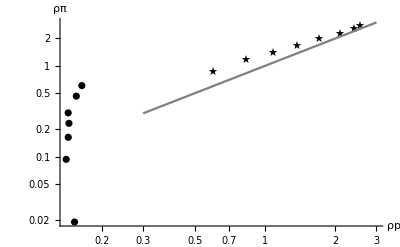

```mathematica
Show[%28,AxesLabel->{HoldForm[ρp],HoldForm[ρπ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Studio inclusivo dello stock di erba. Nuovi colori: Erba = DD@Green, Prede = Brown, Predatori = D@Gray

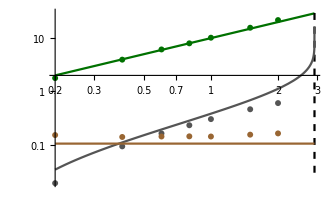

```mathematica
Show[LogLogPlot[ρr[λ,γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Darker[Darker[Green]]],ListLogLogPlot[numr,PlotStyle->Darker[Darker[Green]]],LogLogPlot[ρπ[λ,d,γ,αp],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Darker@Gray],ListLogLogPlot[numπ,PlotStyle->Darker@Gray],LogLogPlot[ρp[γ],{λ,0.2,λc[γ,αp,d]},PlotRange->All,PlotStyle->Brown],ListLogLogPlot[nump,PlotStyle->Brown],ParametricPlot[{Log[λc[γ,αp,d]],x},{x,Log@0.03,Log@30},PlotStyle->{Black,Dashed}],PlotRange->Full]
```